```mathematica
SetDirectory[ToFileName[{$HomeDirectory,"workspace","tanoprojects","quickerrorplot","example"}]];
Needs["QuickErrorPlot`","../QuickErrorPlot.m"]
```

```mathematica
data=Import["Example.xlsx"];
sheets=Import["Example.xlsx","Sheets"];
```

```mathematica
?QuickErrorPlot
```

QuickErrorPlot[ data , <options> ]:
  Creates a simple ErrorListPlot with a Legend.

Data must contain exactly 4 columns - x, y, Δx, Δy, and must be
in a form of sheets: {{{x, y, Δx, Δy}, {...}, ...}, {...}, ...}

This is a list of options that QuickErrorPlot accepts and their
default options. Where multiple options are listed, the first 
is the default:

General:
    Legend      → {},
    LegendPosition → {0.75, -0.3},
    RemoveLines → 0,
    Colors      → 1,
    ColorsStart → 1,

For the Plot:
    Labels        → {"",""},
    Title         → "",
    PlotRange     → Automatic,
    AspectRatio   → 1/GoldenRatio

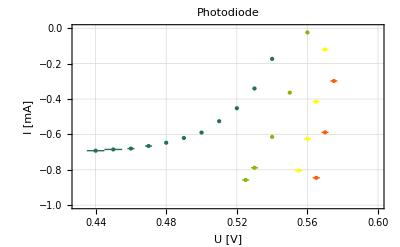

```mathematica
QuickErrorPlot[data,RemoveLinesStart->1,Legend->sheets,PlotRange->{{0.43,.6},{-1,0}},Labels->{"U [V]","I [mA]"},Title->"Photodiode",Colors->3,ColorsStart->2]
```